```mathematica
epsilon=11/9136
```

11/9136

```mathematica
p=0.1
```

0.1

```mathematica
f[x_]:=(epsilon(x-1)+epsilon√((x-1)^2+4*p*x))/(2x)
```

Plot::nonopt: Options expected (instead of {x,0,15}) beyond position 2 in Plot[f[x],g[x],{x,0,15}]. An option must be a rule or a list of rules.

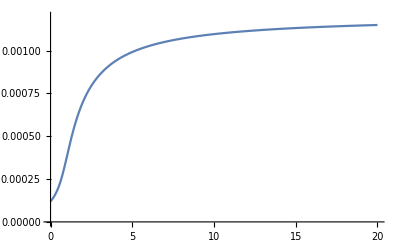

```mathematica
p1=Plot[f[x],{x,0,20},PlotRange->{{0,15}{0,0.00008}}]
```

```mathematica
g[x_]:=epsilon(1-1/x)
```

```mathematica
g[x]
```

(11 (1-1/x))/14611

```mathematica
f[x]
```

((11 √((-1+x)^2+0.4 x))/9136+(11 (-1+x))/9136)/(2 x)

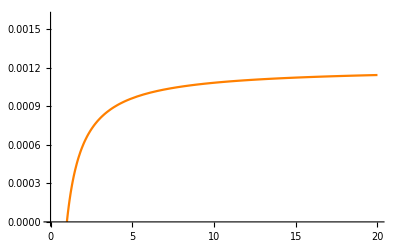

```mathematica
p2=Plot[g[x],{x,0,20},PlotRange->{{0,20}{0,0.00008}},PlotStyle->{Orange}]
```

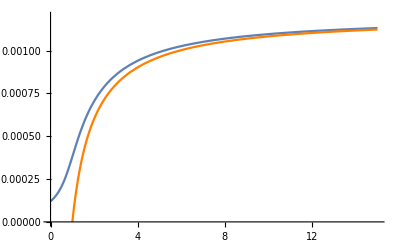

```mathematica
Show[p1,p2]
```

```mathematica
h[x_]:=f[x]/g[x]
```

```mathematica
h[x]
```

(4568 ((11 √((-1+x)^2+0.4 x))/9136+(11 (-1+x))/9136))/(11 (1-1/x) x)

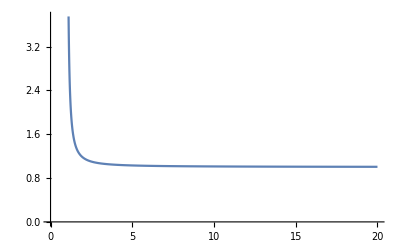

```mathematica
p3=Plot[h[x],{x,0,20},PlotRange->{{0,15}{0,0.25}}]
```

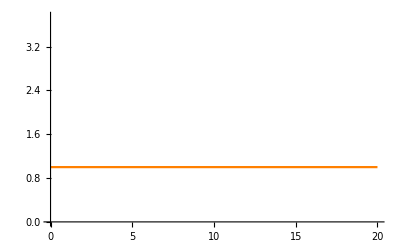

```mathematica
p4=Plot[1,{x,0,20},PlotRange->{{0,15}{0,0.25}},PlotStyle->{Orange}]
```

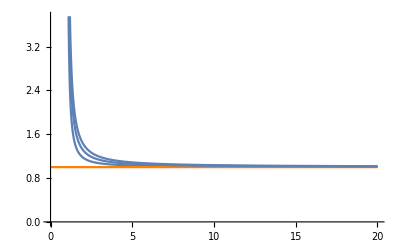

```mathematica
Show[p3,p4,p7,p8]
```

```mathematica
f2[x_]:=(epsilon(x-1)+epsilon√((x-1)^2+4*0.2*x))/(2x)
```

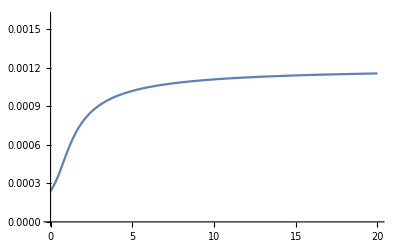

```mathematica
p5=Plot[f2[x],{x,0,20},PlotRange->{{0,20}{0,0.00008}}]
```

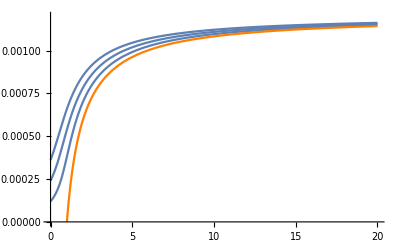

```mathematica
Show[p1,p2,p5,p6]
```

```mathematica
f3[x_]:=(epsilon(x-1)+epsilon√((x-1)^2+4*0.3*x))/(2x)
```

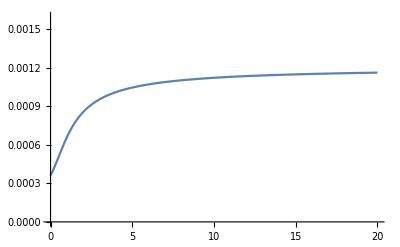

```mathematica
p6=Plot[f3[x],{x,0,20},PlotRange->{{0,20}{0,0.00008}}]
```

```mathematica
h2[x_]:=f2[x]/g[x]
```

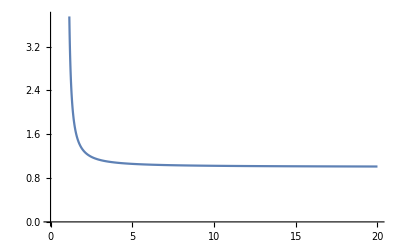

```mathematica
p7=Plot[h2[x],{x,0,20},PlotRange->{{0,15}{0,0.25}}]
```

```mathematica
h3[x_]:=f3[x]/g[x]
```

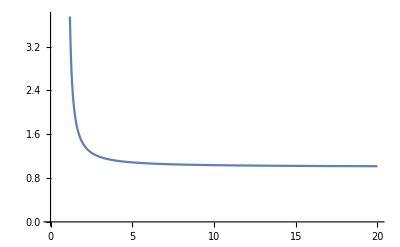

```mathematica
p8=Plot[h3[x],{x,0,20},PlotRange->{{0,15}{0,0.25}}]
```